```mathematica
top3=Import["/Users/nsonmez/Desktop/6.EventGENERATION/2HDMC-1.6.5/top_type3"]⟦All,6⟧//Flatten;
top3p=Table[{i*0.1,top3⟦i⟧},{i,1,top3//Length}];
higgs3=Import["/Users/nsonmez/Desktop/6.EventGENERATION/2HDMC-1.6.5/higgs_type3"]⟦All,6⟧//Flatten;
higgs3p=Table[{i*0.1,higgs3⟦i⟧},{i,1,higgs3//Length}];
top4=Import["/Users/nsonmez/Desktop/6.EventGENERATION/2HDMC-1.6.5/top_type4"]⟦All,6⟧//Flatten;
top4p=Table[{i*0.1,top4⟦i⟧},{i,1,top4//Length}];
higgs4=Import["/Users/nsonmez/Desktop/6.EventGENERATION/2HDMC-1.6.5/higgs_type4"]⟦All,6⟧//Flatten;
higgs4p=Table[{i*0.1,higgs4⟦i⟧},{i,1,higgs4//Length}];
```

```mathematica
Get["MathUtils/LoadPlottingSettings.m"]
```

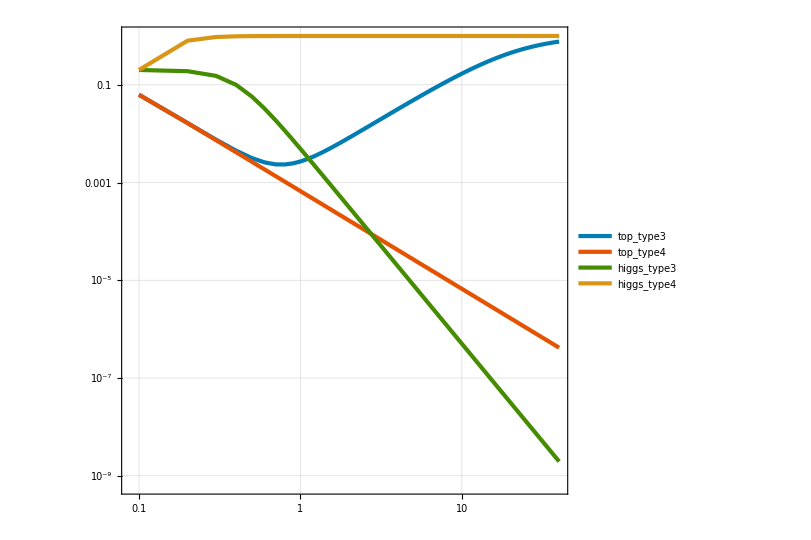

```mathematica
ListLogLogPlot[{top3p,top4p,higgs3p,higgs4p},Joined->True,PlotLegends->LineLegend[{"top_type3","top_type4","higgs_type3","higgs_type4"}]]
```